## NEGF

16

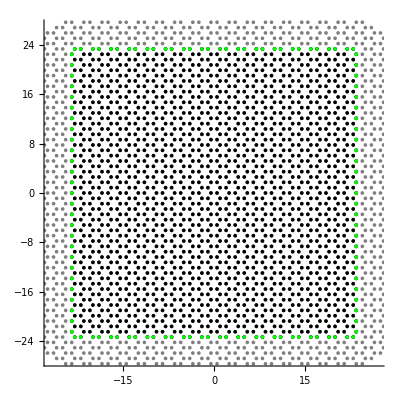

```mathematica
nuc=16
width=3*nuc;height=width;
L=Max[{width,height}];
a=1;L1=L+1;L2=L+1;
a1=a/2{3,√3,0};
a2=a/2{3,-√3,0};
b1={a,0,0};
uc = {0*b1,b1};
latt=Flatten[Table[n1*a1+n2*a2+u,{n1,L1},{n2,L2},{u,uc}],2];
meanPosition=Mean[latt];
latt=(#-meanPosition)&/@latt;
lattRegion=DeleteCases[latt,_?(Not[(-width/2<#[[1]]<width/2)&&(-height/2<#[[2]]<height/2)]&)];
rB=Max[lattRegion[[All,1]]];lB=Min[lattRegion[[All,1]]];
tB=Max[lattRegion[[All,2]]];bB=Min[lattRegion[[All,2]]];
lrPos=Flatten[Position[lattRegion[[All,1]],n_ /; n==#]]&/@{rB,lB};
tbPos=Flatten[Position[lattRegion[[All,2]],n_ /; n==#]]&/@{tB,bB};
bPos=Join[lrPos,tbPos];
Graphics[{{{Directive[Opacity[0.5],Black],Disk[#[[1;;2]],0.3]}&/@latt},{{Black,Disk[#[[1;;2]],0.3]}&/@lattRegion},{{Green,Disk[#[[1;;2]],0.3]}&/@lattRegion[[#]]&/@bPos}},ViewPoint->Top,Axes->True,PlotRange->{{-width/2-3,width/2+3},{-height/2-3,height/2+3}}]
latt=lattRegion;
dimH = Length[latt];
```

```mathematica
dist[n1_,n2_]:=Norm[n2-n1];
dists=Outer[dist,latt,latt,1];
```

```mathematica
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
```

```mathematica
neighbors=Position[dists,#,3]&/@ddists[[;;3]];
```

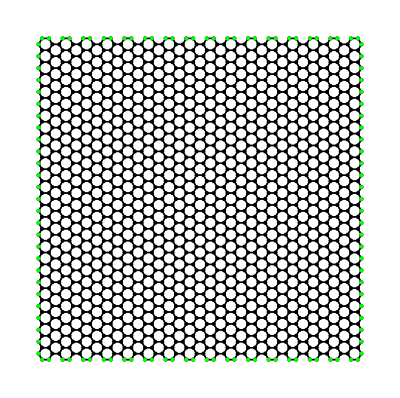

```mathematica
Graphics[{{{Black,CapForm["Butt"],Line[{latt[[#[[1]],1;;2]],latt[[#[[2]],1;;2]]}]}&/@neighbors[[2]]},{Black,Disk[#[[1;;2]],0.3]}&/@latt,{{Green,Disk[#[[1;;2]],0.3]}&/@lattRegion[[#]]&/@bPos}},ViewPoint->Top]
(*Graphics3D[{{{Black,CapForm["Butt"],Tube[{latt[[#[[1]]]],latt[[#[[2]]]]},.1]}&/@neighbors[[2]]},{Black,Sphere[#,0.3]}&/@latt},ViewPoint->Top];*)
```

Eigensystem::arh: Because finding 1760 out of the 1760 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

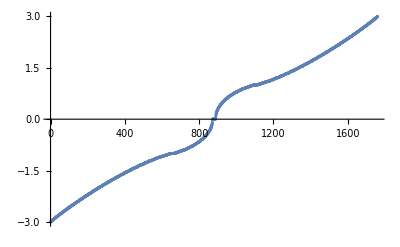

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];
H = SparseArray[#-> 1.0&/@neighbors[[2]]];
{energies,wavefunctions}=orderedEigensystem[H]//Sort;
imEnergies=Im[energies];
energies=Re[energies];
ListPlot[energies]
max=Max[energies];min=Min[energies];
(*Histogram[energies,{min,max,(max-min)/54},"Probability",PlotRange->{{-1.5,1.5},Automatic}]*)
```

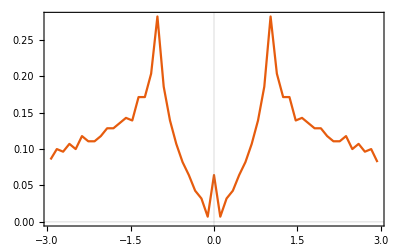

```mathematica
{bene,bvals}=HistogramList[energies,{min,max,(max-min)/53},Probability];
ListPlot[{MovingAverage[bene,2],bvals*2*π}ᵀ,Joined->True,PlotTheme->"Scientific"]
```

```mathematica
η=0.05;
Gs={};
ees=Range[-3,3,0.01];
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)]
Monitor[
Do[
AppendTo[Gs,Inverse[N[H-ee*IdentityMatrix[Dimensions[H]]-Σ]]];
,{ee,ees}],ee]
```

SparseArray[…]

$Aborted

```mathematica
Clear[BlockAverage]
BlockAverage[xs_,r_]:=Table[Mean[xs[[i;;i+r]]],{i,1,Length[xs]-r,r}]
```

```mathematica
As=Plus@@Re[Diagonal[-ⅈ*(#-#†)]]&/@Gs;
As/=Plus@@As;
```

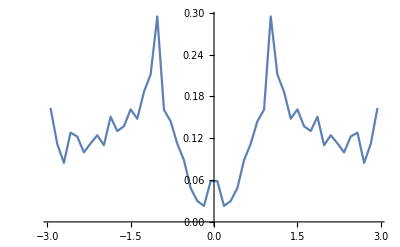

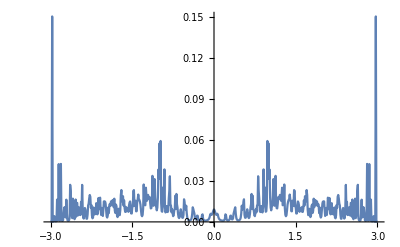

```mathematica
rBlock=IntegerPart[Length[ees]/50];
mAs=BlockAverage[As,rBlock];
mees=BlockAverage[ees,rBlock];
mAs/=Plus@@mAs;
ListPlot[{mees,mAs 2π}ᵀ,Joined->True,PlotRange->Full]
ListPlot[{ees,As 2π}ᵀ,Joined->True,PlotRange->Full]
```